```mathematica
Nb0 = SelectedNotebook[];
μList={};
AList={};
λList={};
ϕList={};
OffsetList1={};
OffsetList2={};
```

```mathematica
Do[
pwd=NotebookDirectory[];
Nb1=NotebookOpen[pwd<>"/Test"<>ToString[Ntest]<>".nb",Visible->False];
NotebookFind[Nb1,"Abasis"];
SelectionMove[Nb1,All,CellContents];
SelectionMove[Nb1,All,Word];
Do[FrontEndExecute[FrontEndToken[Nb1,"SelectNextLine"]],4];
FrontEndExecute[FrontEndToken[Nb1,"SelectLineEnd"]];
FrontEndExecute[FrontEndToken[Nb1,"CellSplit"]];
SelectionMove[Nb1,Previous,CellContents];
FrontEndExecute[FrontEndToken[Nb1,"Copy"]];
FrontEndExecute[FrontEndToken[Nb0,"Paste"]];
NotebookFind[Nb1,"EndFailOffset"];
FrontEndExecute[FrontEndToken[Nb1,"SelectLineEnd"]];
FrontEndExecute[FrontEndToken[Nb1,"Copy"]];
FrontEndExecute[FrontEndToken[Nb0,"Paste"]];
NotebookWrite[Nb0,"
AppendTo[μList,μ0B];
AppendTo[AList,Abasis];
AppendTo[λList,λbasis];
AppendTo[ϕList,ϕbasis];
AppendTo[OffsetList1,LengthOffset];
AppendTo[OffsetList2,EndFailOffset];"];
SelectionMove[Nb0,All,CellContents];
SelectionEvaluate[Nb0];
NotebookClose[Nb1];,{Ntest,22}]
```

```mathematica
μ0B=0.48;
Abasis = 0.1;
λbasis=0.0021;
ϕbasis=0*π/2;
LengthOffset=10;EndFailOffset=0.00;
AppendTo[μList,μ0B];
AppendTo[AList,Abasis];
AppendTo[λList,λbasis];
AppendTo[ϕList,ϕbasis];
AppendTo[OffsetList1,LengthOffset];
AppendTo[OffsetList2,EndFailOffset];
```

```mathematica
μ0B=0.48;
Abasis = 0.1;
λbasis=0.0021;
ϕbasis=0*π/2;
LengthOffset=10;EndFailOffset=0.00;
AppendTo[μList,μ0B];
AppendTo[AList,Abasis];
AppendTo[λList,λbasis];
AppendTo[ϕList,ϕbasis];
AppendTo[OffsetList1,LengthOffset];
AppendTo[OffsetList2,EndFailOffset];
```

```mathematica
μList
AList
λList
ϕList
OffsetList1
OffsetList2
```

{0.5,0.4,0.47,0.7,0.55,0.334,0.3,0.184,0.4,0.41,0.28,0.3,0.42,0.63,0.2,0.42,0.4,0.41,0.54,0.38,0.3,0.48}

{0.03,0.032,0.02,0.12,0.02,0.016,0.043,0.065,0.035,0.05,0.03,0.07,0.05,0.03,0.03,0.07,0.022,0.03,0.07,0.1,0.03,0.1}

{0.002,0.015,0.01,0.002,0.002,0.0014,0.004,0.004,0.01,0.003,0.012,0.0017,0.015,0.006,0.0018,0.015,0.01,0.0027,0.0034,0.0064,0.0015,0.0021}

{2.67035,1.88496,-π/2,2.32743,1.88496,0,0.,1.25664,5.65487,-π/2,π/2,π/2,-π/2,π/2,0,π,3.92699,π/2,-3.92699,(3 π)/2,π/2,0}

{-10,-25,-25,-10,-10,-10,0,0,-20,-15,-15,-10,-70,-120,0,0,-5,-5,-8,-50,-13,10}

{0.02,-0.01,0.,-0.057,-0.025,0.02,0.04,0.07,-0.035,0.095,0.09,0.1,-0.036,-0.05,0.13,-0.05,0.01,0.015,-0.032,0.028,-0.06,0.}

```mathematica
μList={0.5,0.4,0.47,0.7,0.55,0.334,0.3,0.184,0.4,0.41,0.28,0.3,0.42,0.63,0.2,0.42,0.4,0.41,0.54,0.38,0.3,0.48}
AList={0.03,0.032,0.02,0.12,0.02,0.016,0.043,0.065,0.035,0.05,0.03,0.07,0.05,0.03,0.03,0.07,0.022,0.03,0.075,0.1,0.11,0.1}
λList={0.002,0.015,0.01,0.002,0.002,0.0014,0.004,0.004,0.01,0.003,0.012,0.0017,0.015,0.006,0.0018,0.015,0.01,0.0027,0.0034,0.0064,0.02,0.0021}
ϕList={2.670353755551324,1.8849555921538759,-π/2,2.327433388230814,1.8849555921538759,0,0.,1.2566370614359172,5.654866776461628,-π/2,π/2,π/2,-π/2,π/2,0,π,3.9269908169872414,π/2,-3.9269908169872414,(3 π)/2,π,0}
OffsetList1={-10,-25,-25,-10,-10,-10,0,0,-20,-15,-15,-10,-70,-120,0,0,-5,-5,-8,-50,0,10}
OffsetList2={0.02,-0.01,0.,-0.057,-0.025,0.02,0.04,0.07,-0.035,0.095,0.09,0.1,-0.036,-0.05,0.13,-0.05,0.01,0.015,-0.032,0.028,-0.05,0.}
```

{0.5,0.4,0.47,0.7,0.55,0.334,0.3,0.184,0.4,0.41,0.28,0.3,0.42,0.63,0.2,0.42,0.4,0.41,0.54,0.38,0.3,0.48}

{0.03,0.032,0.02,0.12,0.02,0.016,0.043,0.065,0.035,0.05,0.03,0.07,0.05,0.03,0.03,0.07,0.022,0.03,0.075,0.1,0.11,0.1}

{0.002,0.015,0.01,0.002,0.002,0.0014,0.004,0.004,0.01,0.003,0.012,0.0017,0.015,0.006,0.0018,0.015,0.01,0.0027,0.0034,0.0064,0.02,0.0021}

{2.67035,1.88496,-π/2,2.32743,1.88496,0,0.,1.25664,5.65487,-π/2,π/2,π/2,-π/2,π/2,0,π,3.92699,π/2,-3.92699,(3 π)/2,π,0}

{-10,-25,-25,-10,-10,-10,0,0,-20,-15,-15,-10,-70,-120,0,0,-5,-5,-8,-50,0,10}

{0.02,-0.01,0.,-0.057,-0.025,0.02,0.04,0.07,-0.035,0.095,0.09,0.1,-0.036,-0.05,0.13,-0.05,0.01,0.015,-0.032,0.028,-0.05,0.}

### Range of the parameters

```mathematica
Max@μList
Min@μList
```

0.7

0.184

```mathematica
Max@(AList/μList)
Min@(AList/μList)
```

0.353261

0.0363636

```mathematica
Max@λList*1250*2π
Min@λList*1250*2π
```

117.81

10.9956

```mathematica
Max@ϕList
Min@ϕList
```

5.65487

-3.92699

### Plotting

```mathematica
SetDirectory[NotebookDirectory[]];
Get<<"../data/SolutionVector2_Feb3";
SolutionVector01=SolutionVector2/.Null->Nothing;
BendTests=Import["../data/201708_BendTests_SS_processed_data_Info.mat"];
Bendlabels=Import["../data/201708_BendTests_SS_processed_data_Info.mat","Labels"]
BendTestAll=Import["../data/201708_BendTests_SS_processed_data_Fw0.mat"];
BendlabelAll=Import["../data/201708_BendTests_SS_processed_data_Fw0.mat","Labels"]
force= BendTestAll[[Position[BendlabelAll,"force"][[1,1]] ]];
dflctn= BendTestAll[[Position[BendlabelAll,"dflctn"][[1,1]] ]];
Bstif=Flatten[ BendTests[[Position[Bendlabels,"Bstif"][[1,1]] ]]];(*EI/L^3*)
Kcant=Flatten[ BendTests[[Position[Bendlabels,"Kcant"][[1,1]] ]]];
w0slp=Flatten[ BendTests[[Position[Bendlabels,"w0slp"][[1,1]] ]]];
w0star=Flatten[ BendTests[[Position[Bendlabels,"w0star"][[1,1]] ]]];
wsslp=Flatten[ BendTests[[Position[Bendlabels,"w_sslp"][[1,1]] ]]];
wsstar=Flatten[ BendTests[[Position[Bendlabels,"w_sstar"][[1,1]] ]]];
L=Flatten[ BendTests[[Position[Bendlabels,"L"][[1,1]] ]]];
SSpattern=Flatten[ BendTests[[Position[Bendlabels,"SSpattern"][[1,1]] ]]];
Pslip=Flatten@Position[SSpattern,True];
Pcontinue =Flatten@Position[SSpattern[[;;38]],False];
w0slpN=(w0slp/L)[[Pslip]];
w0starN=(w0star/L)[[Pslip]];
StageDis=(wsslp/L)[[Pslip]];
FailDis=(wsstar/L)[[Pslip]];
OblSlope=(Kcant/Bstif)[[Pslip]];
fw0All=Table[{dflctn[[i,j]]/L[[i]],force[[i,j]]/Bstif[[i]]/L[[i]]},{i,38},{j,Length@force[[i]]}];
fw0=fw0All[[Pslip]];
FailureIndex=Table[Length@Select[fw0[[i,;;,1]],0<#≤w0starN[[i]]&],{i,Length@w0starN}];
```

{Bstif,D,E,Fslp,Fstar,K_s,Kc_SE,Kcant,L,N_L,SSpattern,axL,dSstar,evbool,indx_fail,indx_slp,sD,s_L,w0slp,w0star,w_sslp,w_sstar}

{Fslp,Fstar,dflctn,dsplcmnt,force}

```mathematica
IndSSTEST=Flatten@Position[SSpattern,True]
```

{4,5,7,8,11,12,14,16,17,18,19,20,22,24,25,26,29,30,32,33,35,38}

```mathematica
EndFail=0.274;
Outline[text_]:=First@ImportString[ExportString[text,"PDF"],"PDF","TextMode"->"Outlines"]
```

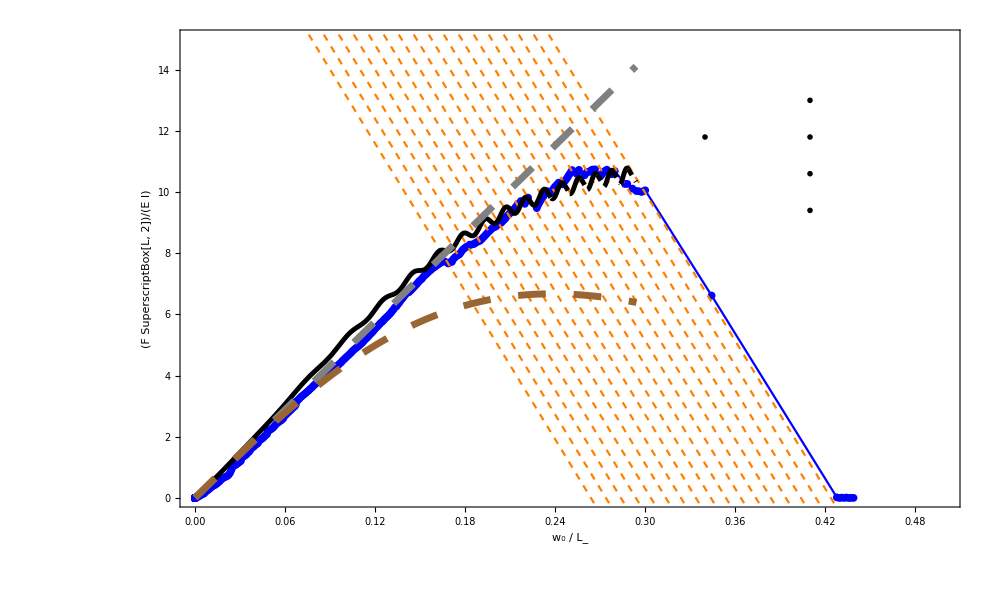
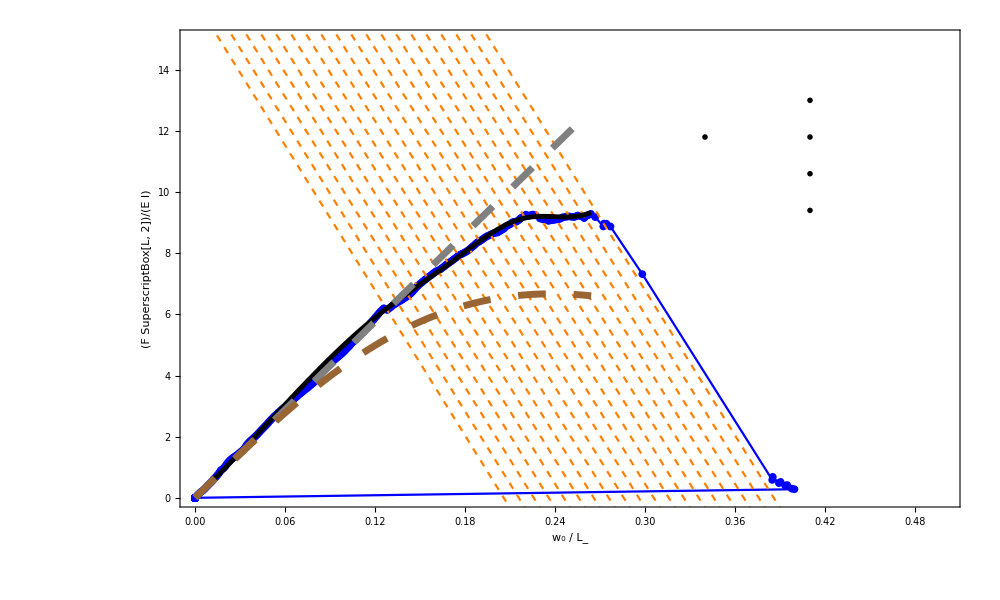
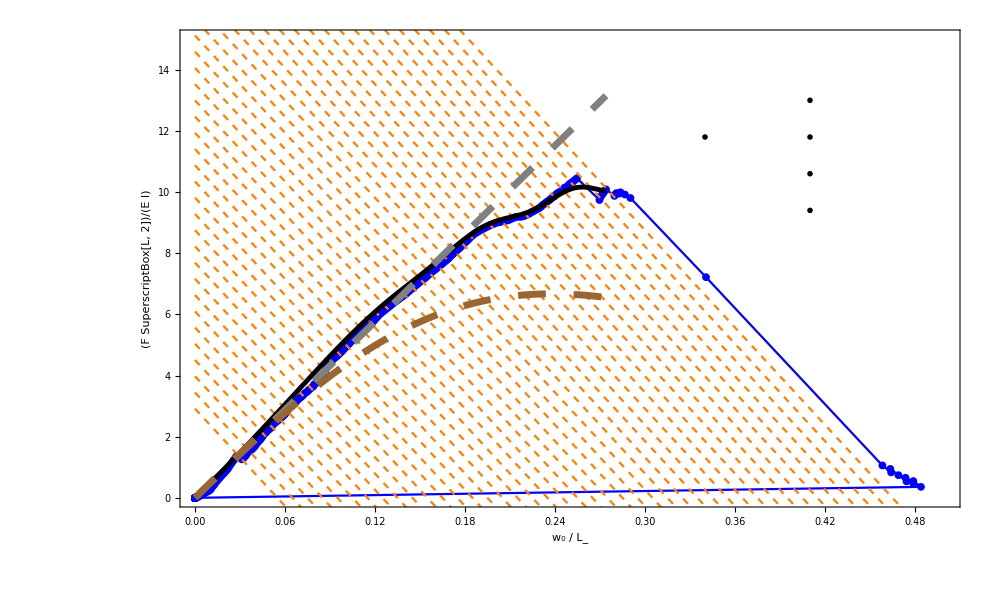
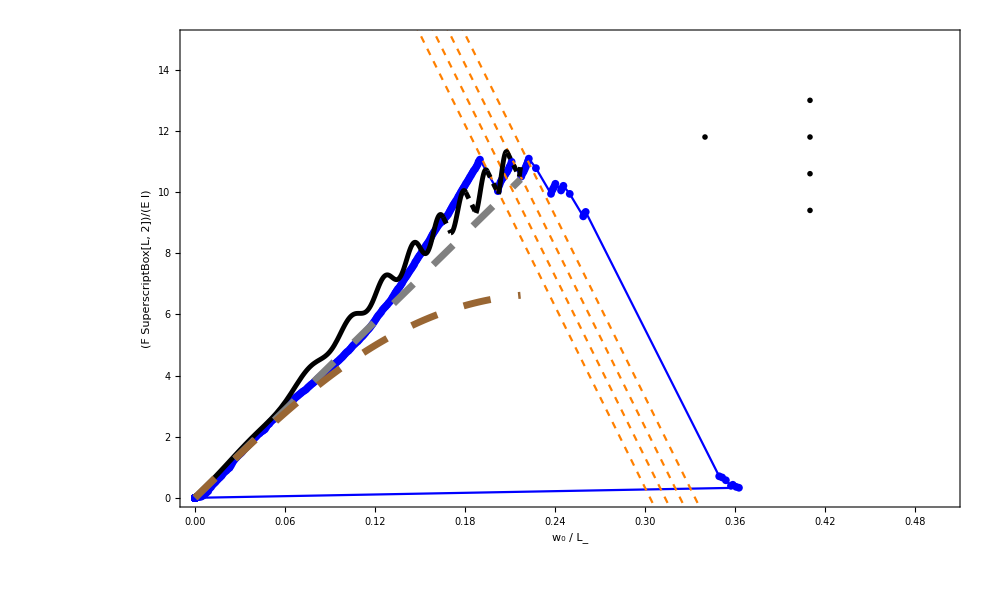
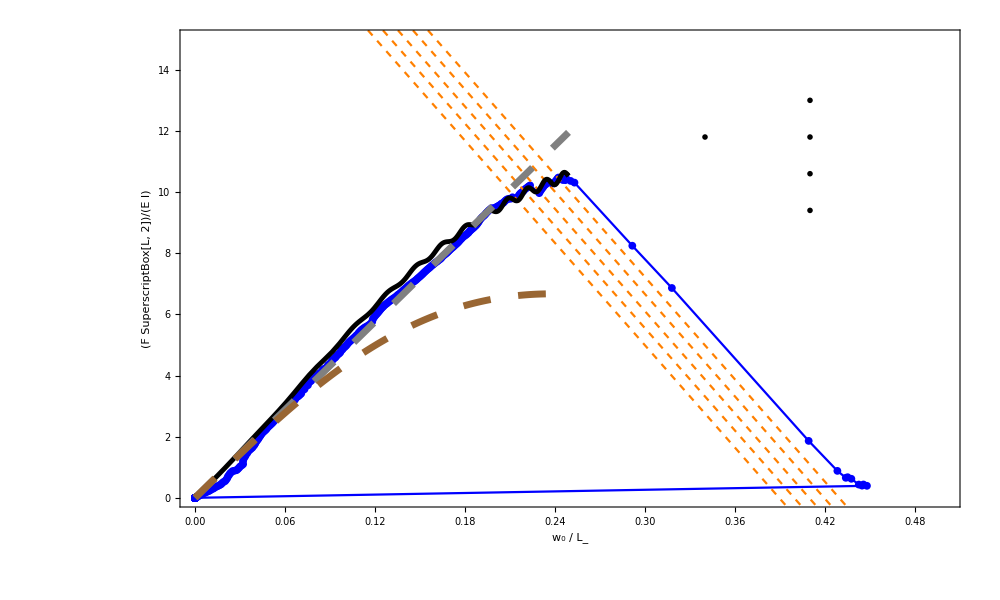
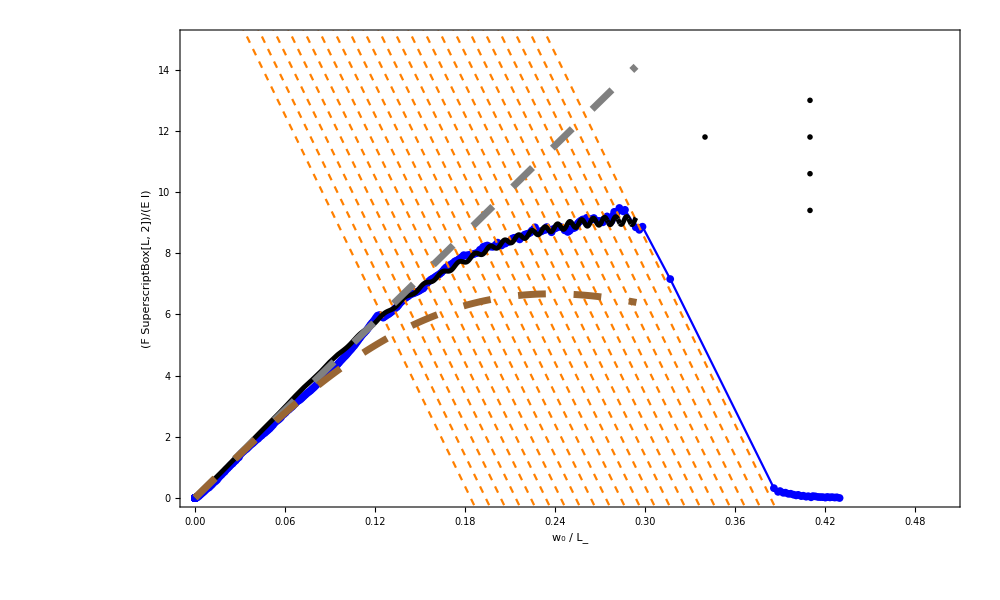
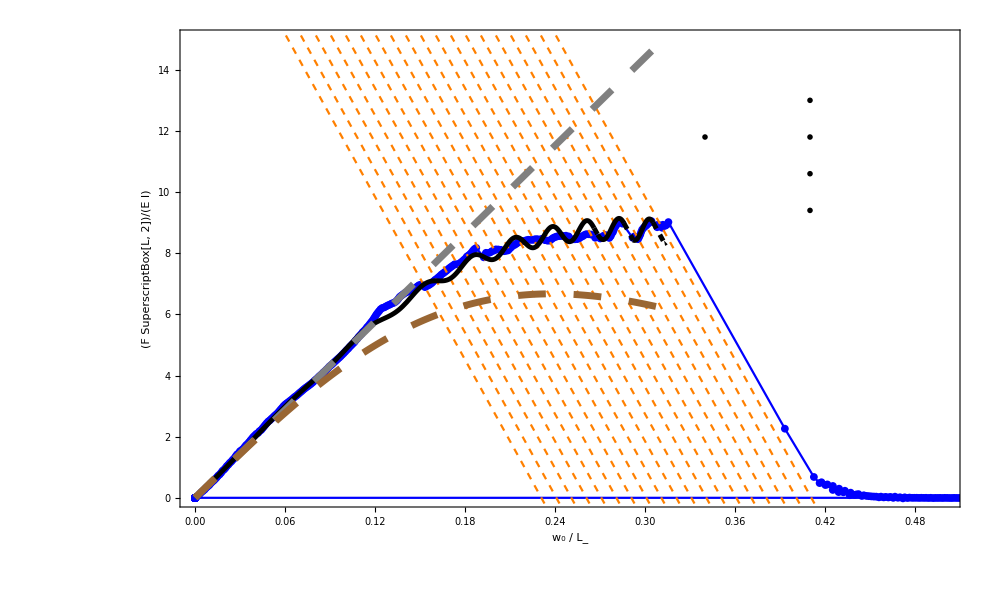
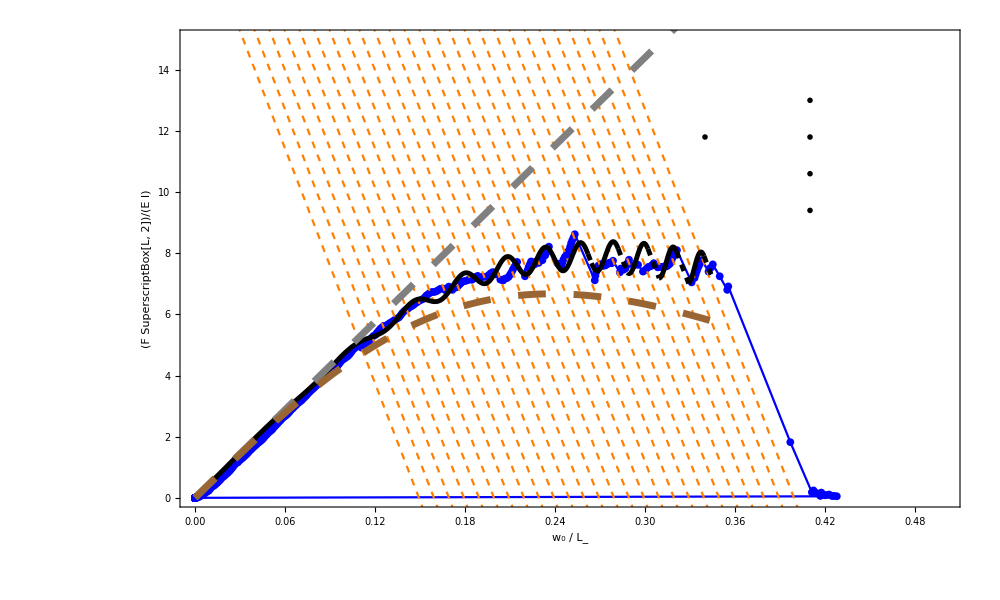

```mathematica
AllPlot=Table[(*NTest=6;*)
μ0B=μList[[NTest]];
Abasis = AList[[NTest]];
λbasis=λList[[NTest]];
ϕbasis=ϕList[[NTest]];
LengthOffset=OffsetList1[[NTest]];
PSingleExp=Module[{n=NTest,P1,P2,P3},
P1 = ListPlot[fw0[[n]],PlotMarkers->{Automatic,8},PlotRange->{{0.0,0.5},{0,15}},PlotStyle->Blue,
(*ImageSize->1200,*)GridLines->None,Ticks->Automatic,Joined->True,
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],
FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},
RotateLabel->False];
P2  = Module[{k = OblSlope[[n]],wss = StageDis[[n]],wsf=FailDis[[n]],Obline},
Obline[x_,wsi_] = k (wsi - x);
Plot[{Obline[x,wss],Obline[x,wsf]}, {x, 0, 0.5},PlotStyle->{Red,Purple}]
];
P3 = Module[{k = OblSlope[[n]],wss = StageDis[[n]],wsf=FailDis[[n]],Obline},
Obline[x_,wsi_] = k (wsi - x);
 Plot[Obline[x,#]&/@Range[wss,wsf,0.01], {x, 0, 0.5},PlotStyle->{Dashed,Orange}]
];
Show[P1,(*P2,*)P3(*,Plot[48x,{x,0,0.5},PlotStyle->{Gray,Dashed}]*)]
];
Module[{μ0={μ0B},A = Abasis,λ=λbasis,ϕ=ϕbasis},
arclength=SolutionVector01[[;;,;;,5]];
frictionC=SolutionVector01[[;;,;;,6]];
levelset=frictionC-A Cos[arclength/λ+ϕ];
FwLevelset=Flatten[Table[{SolutionVector01[[i,j,1]],SolutionVector01[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector01},{j,1,Length[SolutionVector01[[i]]]}],1];
	Levelμ0=Table[Select[FwLevelset,Abs[#[[3]]-i]<10^-3&],{i,μ0}];
Levelμ0S=(SortBy[Levelμ0[[#]],First])&/@Range@Length@μ0;
FailIndex=Length@Select[Levelμ0S[[1,;;,1]],0<#≤w0starN[[NTest]]&]+LengthOffset;];
Off[General::partw];
Lfragf[x_,k_,x0_,y0_]=-k(x-x0)+y0;
xx=fw0[[NTest,;;FailureIndex[[NTest]],1]];
yy=fw0[[NTest,;;FailureIndex[[NTest]],2]];
(*EndFail=xx[[-1]]*)

Posμ0B=μ0B/0.002+1;
fitFw0B=Module[{data1,fit},
data1=SolutionVector01[[Posμ0B,;;,{1,2}]];
fit[x_]=Fit[data1,{x,x^2,x^3,x^4,x^5,x^6},x];
Function[x,fit[x]]
];
fitSw0B=Module[{data1,fit},
data1=SolutionVector01[[Posμ0B,;;,{1,5}]];
fit[x_]=Fit[data1,{1,x,x^2,x^3},x];
Function[x,fit[x]]
];
fitVariation=Module[{ λ=λbasis,ϕ=ϕbasis,xx1,yy1,data1,ABF},
xx1=fitSw0B/@Levelμ0S[[1,;;,1]];
yy1=Levelμ0S[[1,;;,2]]-fitFw0B/@Levelμ0S[[1,;;,1]];
data1=Transpose@{xx1,yy1};
ABF=FindFit[data1,(B1 x +B2 x^2 +B3 x^3 +B4 x^4 + B5 x^5+B6 x^6   +B7 x^7 +B8 x^8 )Cos[x/λ+ϕ],{B1,B2,B3,B4,B5,B6,B7,B8},x];
Function[x,Evaluate[(B1 x +B2 x^2 +B3 x^3 +B4 x^4 + B5 x^5 +B6 x^6 +B7 x^7 +B8 x^8 (*+B9 x^9+B10 x^10*) )Cos[x/λ+ϕ]/.ABF]]
];
EndFailOffset=OffsetList2[[NTest]];
Pffrag=Module[{f,IntSecPxSol,IntSecPx,IntSecPxy,IntSecP,LIntSecPxSol,LIntSecPx,LIntSecPxy,LIntSecP,Lfrag,LfragArray,LfragRange,ffragRangeFront,ffragRange},
f[x_]=Simplify[Through[(Composition[fitVariation,fitSw0B]+fitFw0B)[x]]];
IntSecPxSol=NSolve[{f'[x]==-OblSlope[[NTest]],0<x<EndFail+EndFailOffset},x];
IntSecPx=x/.#&/@IntSecPxSol[[;;;;2]];
IntSecPxy={x,f[x]}/.#&/@IntSecPxSol[[;;;;2]];
LIntSecPxSol=(NSolve[{f[x]==Lfragf[x,OblSlope[[NTest]],IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPxy[[#,1]]+10^-5<x<EndFail+EndFailOffset},x][[1]])&/@Range[Length@IntSecPxy];
ind=0;
If[LIntSecPxSol[[-1]]=={}[[1]],ind=1;LIntSecPxSol[[-1]]={x->EndFail+EndFailOffset}];
LIntSecPx=x/.#&/@LIntSecPxSol;
LIntSecPxy={x,f[x]}/.#&/@LIntSecPxSol;
Lfrag[x_]=({Lfragf[x,OblSlope[[NTest]],IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPx[[#]]<x<LIntSecPx[[#]]})&/@Range@Length@IntSecPx;
ffrag=Simplify@Function[x,Evaluate@Piecewise[Lfrag[x],f[x]]];
(*The below commands are only for plotting*)
IntSecP=Point[IntSecPxy];
LIntSecP=Point[LIntSecPxy];
LfragArray=Function[x,Lfragf[x,OblSlope[[NTest]],IntSecPxy[[#,1]],IntSecPxy[[#,2]]]]&/@Range@Length@IntSecPx;
LfragRange={IntSecPx[[#]],LIntSecPx[[#]]}&/@Range@Length@IntSecPx;
ffragRangeFront=Prepend[{LIntSecPx[[#]],IntSecPx[[#+1]]}&/@Range@(Length@LIntSecPx-1),{0,IntSecPx[[1]]}];
If[ind==1,ffragRange=ffragRangeFront,ffragRange=Append[ffragRangeFront,{LIntSecPx[[-1]],EndFail+EndFailOffset}]];
(*The following statement can be commented for fig 19*)
If[Length@ffragRange==2,ffragRange={{0,EndFail+EndFailOffset}}];
Show[(*Plot[{f[x],Lfragf[x,OblSlope[[NTest]],#[[1]],#[[2]]]&/@IntSecPxy},{x,0,EndFail+EndFailOffset},PlotRange->{{0,EndFail+EndFailOffset},{0,15}},ImageSize->1000,PlotStyle->{Directive[Green,Thickness[0.005],Opacity[0.3]],Orange}]*)
(*,Graphics[{Red,PointSize[0.008],IntSecP}]
,Graphics[{Green,PointSize[0.008],LIntSecP}]*)
(*,*)Plot[LfragArray[[#]][x],{x,LfragRange[[#,1]],LfragRange[[#,2]]},PlotStyle->{Black,Thickness[0.0035],Dashed}]&/@Range@Length@LfragArray
,Plot[f[x],{x,#[[1]],#[[2]]},PlotStyle->{Black,Thickness[0.0035]}]&/@ffragRange
]
(*The above commands are only for plotting*)
];
PEB = Plot[48 x,{x,0,EndFail+EndFailOffset},PlotStyle->{Gray,Dashing[0.02],Thickness[0.005]}];
EndP=Position[SolutionVector01[[1,;;,1]],x_/;x>EndFail+EndFailOffset][[1]];
PEE= ListLinePlot[SolutionVector01[[1,;;EndP[[1]],{1,2}]],PlotStyle->{Brown,Dashing[0.02],Thickness[0.005]}];
     TextPx = 0.41;
TextPy = 13;
TextPyOffSet=1.2;
PCOMSS22=Show[
PSingleExp,
Pffrag,
PEB,
PEE,
(*Graphics[{Red,Thickness[0.0015],Line[{{boxx1,boxy1},{boxx2,boxy1},{boxx2,boxy2},{boxx1,boxy2},{boxx1,boxy1}}]}],*)
Graphics[{Text[Outline@Style["Test No.
  SS"<>IntegerString[IndSSTEST[[NTest]]],Black,FontFamily->"Times",28/(23/32)],{TextPx-0.07,TextPy-TextPyOffSet},{-1,0}],
Text[Outline@Style["μ_0 = "<>ToString[NumberForm[μ0B,{3,3}]],Black,FontFamily->"Times",28/(23/32)],{TextPx,TextPy},{-1,0}],
Text[Outline@Style["Â = "<>ToString[NumberForm[Abasis/μ0B,{3,3}]],Black,FontFamily->"Times",28/(23/32)],{TextPx,TextPy-TextPyOffSet},{-1,0}],
Text[Outline@Style["λ = "<>ToString[NumberForm[λbasis*1250*2π,{3,1}]]<>" μm",Black,FontFamily->"Times",28/(23/32)],{TextPx,TextPy-2TextPyOffSet},{-1,0}],
Text[Outline@Style["ϕ = "<>ToString[NumberForm[N@ϕbasis,{3,3}]],Black,FontFamily->"Times",28/(23/32)],{TextPx,TextPy-3TextPyOffSet},{-1,0}]}],
(*Epilog->Inset[
Show[PSingleExp,
Plot[LfragArray[[#]][x],{x,LfragRange[[#,1]],LfragRange[[#,2]]},PlotStyle->{Black,Thickness[0.009],Dashing[0.02]}]&/@Range@Length@LfragArray,
Plot[f[x],{x,#[[1]],#[[2]]},PlotStyle->{Black,Thickness[0.009]}]&/@ffragRange,
PlotRange->{{boxx1,boxx2},{boxy1,boxy2}},FrameLabel->None,FrameTicks->None,FrameStyle->Directive[Red,Thick,FontFamily->"Times",28],ImageSize->400,AspectRatio->0.4]
,{0.08,11}],*)
AspectRatio->0.6,ImageSize->1000
]
,{NTest,22}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/research/Spicule slip/Wfiles/supplementary

```mathematica
Export["ComparisonThreeModels/Fitting"<>IntegerString[#,10,2]<>".pdf",AllPlot[[#]]]&/@Range@22
```

{ComparisonThreeModels/Fitting01.pdf,ComparisonThreeModels/Fitting02.pdf,ComparisonThreeModels/Fitting03.pdf,ComparisonThreeModels/Fitting04.pdf,ComparisonThreeModels/Fitting05.pdf,ComparisonThreeModels/Fitting06.pdf,ComparisonThreeModels/Fitting07.pdf,ComparisonThreeModels/Fitting08.pdf,ComparisonThreeModels/Fitting09.pdf,ComparisonThreeModels/Fitting10.pdf,ComparisonThreeModels/Fitting11.pdf,ComparisonThreeModels/Fitting12.pdf,ComparisonThreeModels/Fitting13.pdf,ComparisonThreeModels/Fitting14.pdf,ComparisonThreeModels/Fitting15.pdf,ComparisonThreeModels/Fitting16.pdf,ComparisonThreeModels/Fitting17.pdf,ComparisonThreeModels/Fitting18.pdf,ComparisonThreeModels/Fitting19.pdf,ComparisonThreeModels/Fitting20.pdf,ComparisonThreeModels/Fitting21.pdf,ComparisonThreeModels/Fitting22.pdf}

```mathematica
Min[λList*1250]
```

1.75

#### Plot the 19th fitting graph

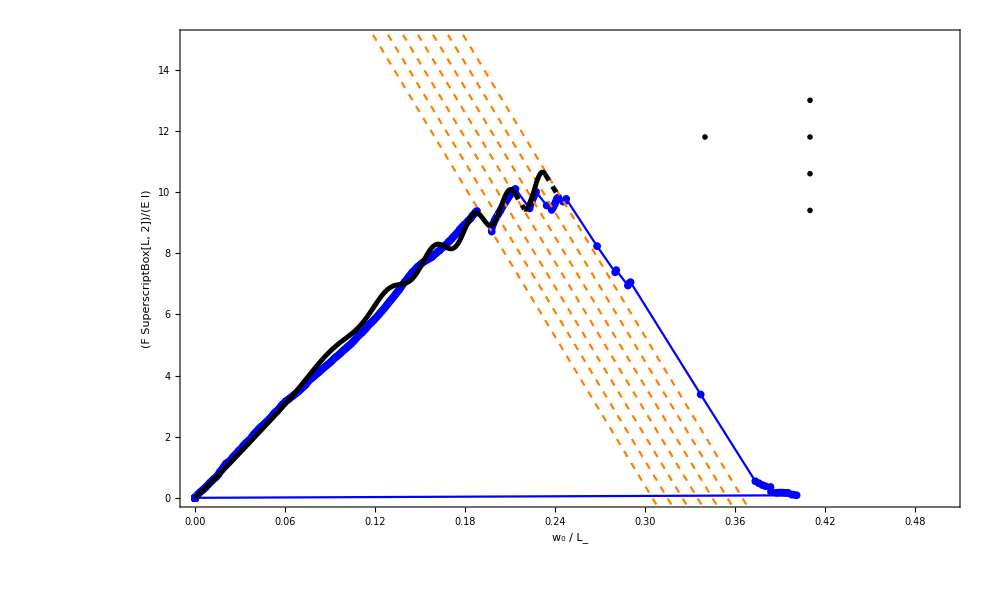

```mathematica
Plot19=Module[{NTest=19},
μ0B=μList[[NTest]];
Abasis = AList[[NTest]];
λbasis=λList[[NTest]];
ϕbasis=ϕList[[NTest]];
LengthOffset=OffsetList1[[NTest]];
PSingleExp=Module[{n=NTest,P1,P2,P3},
P1 = ListPlot[fw0[[n]],PlotMarkers->{Automatic,8},PlotRange->{{0.0,0.5},{0,15}},PlotStyle->Blue,
(*ImageSize->1200,*)GridLines->None,Ticks->Automatic,Joined->True,
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],
FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},
RotateLabel->False];
P2  = Module[{k = OblSlope[[n]],wss = StageDis[[n]],wsf=FailDis[[n]],Obline},
Obline[x_,wsi_] = k (wsi - x);
Plot[{Obline[x,wss],Obline[x,wsf]}, {x, 0, 0.5},PlotStyle->{Red,Purple}]
];
P3 = Module[{k = OblSlope[[n]],wss = StageDis[[n]],wsf=FailDis[[n]],Obline},
Obline[x_,wsi_] = k (wsi - x);
 Plot[Obline[x,#]&/@Range[wss,wsf,0.01], {x, 0, 0.5},PlotStyle->{Dashed,Orange}]
];
Show[P1,(*P2,*)P3(*,Plot[48x,{x,0,0.5},PlotStyle->{Gray,Dashed}]*)]
];
Module[{μ0={μ0B},A = Abasis,λ=λbasis,ϕ=ϕbasis},
arclength=SolutionVector01[[;;,;;,5]];
frictionC=SolutionVector01[[;;,;;,6]];
levelset=frictionC-A Cos[arclength/λ+ϕ];
FwLevelset=Flatten[Table[{SolutionVector01[[i,j,1]],SolutionVector01[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector01},{j,1,Length[SolutionVector01[[i]]]}],1];
	Levelμ0=Table[Select[FwLevelset,Abs[#[[3]]-i]<10^-3&],{i,μ0}];
Levelμ0S=(SortBy[Levelμ0[[#]],First])&/@Range@Length@μ0;
FailIndex=Length@Select[Levelμ0S[[1,;;,1]],0<#≤w0starN[[NTest]]&]+LengthOffset;];
Off[General::partw];
Lfragf[x_,k_,x0_,y0_]=-k(x-x0)+y0;
xx=fw0[[NTest,;;FailureIndex[[NTest]],1]];
yy=fw0[[NTest,;;FailureIndex[[NTest]],2]];
(*EndFail=xx[[-1]]*)

Posμ0B=μ0B/0.002+1;
fitFw0B=Module[{data1,fit},
data1=SolutionVector01[[Posμ0B,;;,{1,2}]];
fit[x_]=Fit[data1,{x,x^2,x^3,x^4,x^5,x^6},x];
Function[x,fit[x]]
];
fitSw0B=Module[{data1,fit},
data1=SolutionVector01[[Posμ0B,;;,{1,5}]];
fit[x_]=Fit[data1,{1,x,x^2,x^3},x];
Function[x,fit[x]]
];
fitVariation=Module[{ λ=λbasis,ϕ=ϕbasis,xx1,yy1,data1,ABF},
xx1=fitSw0B/@Levelμ0S[[1,;;,1]];
yy1=Levelμ0S[[1,;;,2]]-fitFw0B/@Levelμ0S[[1,;;,1]];
data1=Transpose@{xx1,yy1};
ABF=FindFit[data1,(B1 x +B2 x^2 +B3 x^3 +B4 x^4 + B5 x^5+B6 x^6   +B7 x^7 +B8 x^8 )Cos[x/λ+ϕ],{B1,B2,B3,B4,B5,B6,B7,B8},x];
Function[x,Evaluate[(B1 x +B2 x^2 +B3 x^3 +B4 x^4 + B5 x^5 +B6 x^6 +B7 x^7 +B8 x^8 (*+B9 x^9+B10 x^10*) )Cos[x/λ+ϕ]/.ABF]]
];
EndFailOffset=OffsetList2[[NTest]];
Pffrag=Module[{f,IntSecPxSol,IntSecPx,IntSecPxy,IntSecP,LIntSecPxSol,LIntSecPx,LIntSecPxy,LIntSecP,Lfrag,LfragArray,LfragRange,ffragRangeFront,ffragRange},
f[x_]=Simplify[Through[(Composition[fitVariation,fitSw0B]+fitFw0B)[x]]];
IntSecPxSol=NSolve[{f'[x]==-OblSlope[[NTest]],0<x<EndFail+EndFailOffset},x];
IntSecPx=x/.#&/@IntSecPxSol[[;;;;2]];
IntSecPxy={x,f[x]}/.#&/@IntSecPxSol[[;;;;2]];
LIntSecPxSol=(NSolve[{f[x]==Lfragf[x,OblSlope[[NTest]],IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPxy[[#,1]]+10^-5<x<EndFail+EndFailOffset},x][[1]])&/@Range[Length@IntSecPxy];
ind=0;
If[LIntSecPxSol[[-1]]=={}[[1]],ind=1;LIntSecPxSol[[-1]]={x->EndFail+EndFailOffset}];
LIntSecPx=x/.#&/@LIntSecPxSol;
LIntSecPxy={x,f[x]}/.#&/@LIntSecPxSol;
Lfrag[x_]=({Lfragf[x,OblSlope[[NTest]],IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPx[[#]]<x<LIntSecPx[[#]]})&/@Range@Length@IntSecPx;
ffrag=Simplify@Function[x,Evaluate@Piecewise[Lfrag[x],f[x]]];
(*The below commands are only for plotting*)
IntSecP=Point[IntSecPxy];
LIntSecP=Point[LIntSecPxy];
LfragArray=Function[x,Lfragf[x,OblSlope[[NTest]],IntSecPxy[[#,1]],IntSecPxy[[#,2]]]]&/@Range@Length@IntSecPx;
LfragRange={IntSecPx[[#]],LIntSecPx[[#]]}&/@Range@Length@IntSecPx;
ffragRangeFront=Prepend[{LIntSecPx[[#]],IntSecPx[[#+1]]}&/@Range@(Length@LIntSecPx-1),{0,IntSecPx[[1]]}];
If[ind==1,ffragRange=ffragRangeFront,ffragRange=Append[ffragRangeFront,{LIntSecPx[[-1]],EndFail+EndFailOffset}]];
(*The following statement can be commented for fig 19*)
(*If[Length@ffragRange==2,ffragRange={{0,EndFail+EndFailOffset}}];*)
Show[(*Plot[{f[x],Lfragf[x,OblSlope[[NTest]],#[[1]],#[[2]]]&/@IntSecPxy},{x,0,EndFail+EndFailOffset},PlotRange->{{0,EndFail+EndFailOffset},{0,15}},ImageSize->1000,PlotStyle->{Directive[Green,Thickness[0.005],Opacity[0.3]],Orange}]*)
(*,Graphics[{Red,PointSize[0.008],IntSecP}]
,Graphics[{Green,PointSize[0.008],LIntSecP}]*)
(*,*)Plot[LfragArray[[#]][x],{x,LfragRange[[#,1]],LfragRange[[#,2]]},PlotStyle->{Black,Thickness[0.0035],Dashed}]&/@Range@Length@LfragArray
,Plot[f[x],{x,#[[1]],#[[2]]},PlotStyle->{Black,Thickness[0.0035]}]&/@ffragRange
]
(*The above commands are only for plotting*)
];
PEB = Plot[48 x,{x,0,EndFail+EndFailOffset},PlotStyle->{Gray,Dashing[0.02],Thickness[0.005]}];
EndP=Position[SolutionVector01[[1,;;,1]],x_/;x>EndFail+EndFailOffset][[1]];
PEE= ListLinePlot[SolutionVector01[[1,;;EndP[[1]],{1,2}]],PlotStyle->{Brown,Dashing[0.02],Thickness[0.005]}];
     TextPx = 0.41;
TextPy = 13;
TextPyOffSet=1.2;
PCOMSS22=Show[
PSingleExp,
Pffrag,
(*Graphics[{Red,Thickness[0.0015],Line[{{boxx1,boxy1},{boxx2,boxy1},{boxx2,boxy2},{boxx1,boxy2},{boxx1,boxy1}}]}],*)
Graphics[{Text[Outline@Style["Test No.
  SS"<>IntegerString[IndSSTEST[[NTest]]],Black,FontFamily->"Times",28/(23/32)],{TextPx-0.07,TextPy-TextPyOffSet},{-1,0}],
Text[Outline@Style["μ_0 = "<>ToString[NumberForm[μ0B,{3,3}]],Black,FontFamily->"Times",28/(23/32)],{TextPx,TextPy},{-1,0}],
Text[Outline@Style["Â = "<>ToString[NumberForm[Abasis/μ0B,{3,3}]],Black,FontFamily->"Times",28/(23/32)],{TextPx,TextPy-TextPyOffSet},{-1,0}],
Text[Outline@Style["λ = "<>ToString[NumberForm[λbasis*1250*2π,{3,1}]]<>" μm",Black,FontFamily->"Times",28/(23/32)],{TextPx,TextPy-2TextPyOffSet},{-1,0}],
Text[Outline@Style["ϕ = "<>ToString[NumberForm[N@ϕbasis,{3,3}]],Black,FontFamily->"Times",28/(23/32)],{TextPx,TextPy-3TextPyOffSet},{-1,0}]}],
(*Epilog->Inset[
Show[PSingleExp,
Plot[LfragArray[[#]][x],{x,LfragRange[[#,1]],LfragRange[[#,2]]},PlotStyle->{Black,Thickness[0.009],Dashing[0.02]}]&/@Range@Length@LfragArray,
Plot[f[x],{x,#[[1]],#[[2]]},PlotStyle->{Black,Thickness[0.009]}]&/@ffragRange,
PlotRange->{{boxx1,boxx2},{boxy1,boxy2}},FrameLabel->None,FrameTicks->None,FrameStyle->Directive[Red,Thick,FontFamily->"Times",28],ImageSize->400,AspectRatio->0.4]
,{0.08,11}],*)
AspectRatio->0.6,ImageSize->1000
]
]
```

```mathematica
Export["NewFitting/Fitting19.pdf",Plot19]
```

NewFitting/Fitting19.pdf